```mathematica
a=1;
b=9;
c=1;
h=-3;
g=-1;
f=-3/2;
d=a*b*c+2*f*g*h-a*f^2-b*g^2-c*h^2;
If[d==0,Print["pair of straight line"],If[a==b&&h==0,Print["Circle"],If[a*b-h^2>0,Print["Ellipse"],If[a*b-h^2==0,Print["Parabola"],If[a*b-h^2<0,Print["Hyperbola"]]]]]]
```

Parabola

```mathematica
Y=(20x-60y+7)/√4000;
Print["equation of the axis is ",Simplify[Y==0]]
```

equation of the axis is 7+20 x==60 y

```mathematica
X=(1080x+2520y-351)/(√(1080^2+2520^2));
Print["equation of tangent is ",Simplify[X==0]]
```

equation of tangent is 40 (3 x+7 y)==39

```mathematica
Print["vertex=",Solve[{X==0,Y==0},{x,y}]]
```

vertex={{x→19/640,y→81/640}}

```mathematica
a=1/(360 √58);
Print["focus is ",Solve[{X==a,Y==0},{x,y}]]
```

focus is {{x→29/960,y→73/576}}

```mathematica
Print["equation of directrix is ",Simplify[X==-a]]
```

equation of directrix is 36 (3 x+7 y)==35

```mathematica
Print["equation of latus rectum is ",Simplify[X==a]]
```

equation of latus rectum is 45 (3 x+7 y)==44

```mathematica
Print["Length of latus rectum is ",4a]
```

Length of latus rectum is 1/(90 √58)

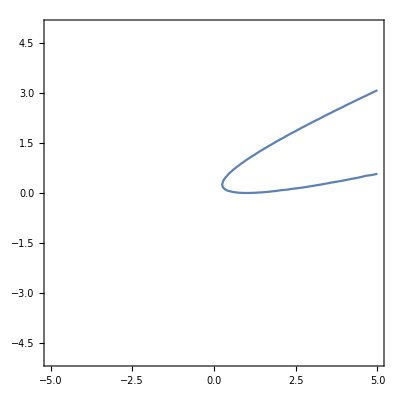

```mathematica
ContourPlot[x^2-6x*y+9 y^2-2x-3y+1==0,{x,-5,5},{y,-5,5}]
```

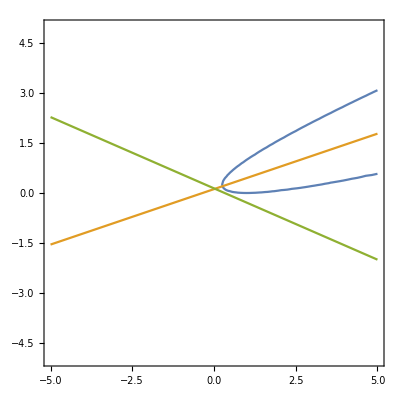

```mathematica
ContourPlot[{x^2-6x*y+9 y^2-2x-3y+1==0,20x-60y+7==0,-351+1080 x+2520 y},{x,-5,5},{y,-5,5}]
```